```mathematica
Needs["nanowire`",NotebookDirectory[]<>"nanowire.wl"]
```

```mathematica
?wfmajoranaqd
```

wfmajoranaqd[a,μ,vz,l0,μm,dim,index]; WF for quantum dots, index for first one or two state(s)

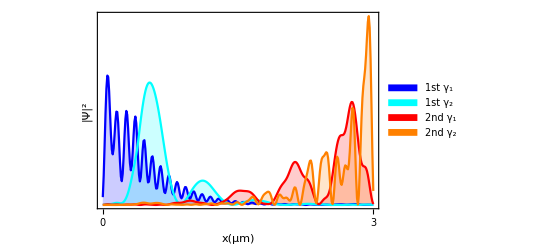

```mathematica
wfm=wfmajoranaqd[1,1,.9,0.6,40,300,2,FrameTicks->{None,{{0,3},None}},FrameLabel->{Style["x(μm)",Directive[Black,30]],Style["|Ψ|^2",Directive[Black,30]]},FrameTicksStyle->Directive[Black,30],PlotLabel->None]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp16\\bad-qd\\1\\m1.0D0.2a5L300VD0.6dL40V0.9.png",wfm]
```

D:\CMTC\bothlead\Rp16\bad-qd\1\m1.0D0.2a5L300VD0.6dL40V0.9.png

```mathematica
?wfmajoranaseqd
```

wfmajoranaseqd[a_,μ_,vz_,μmax_,l0_,γ_,ω_,Vc_,dim_,index_];WF for quantum dots and self energy

ω0=0.01356ω1=0.0136877

ω0=0.048ω1=0.0450009

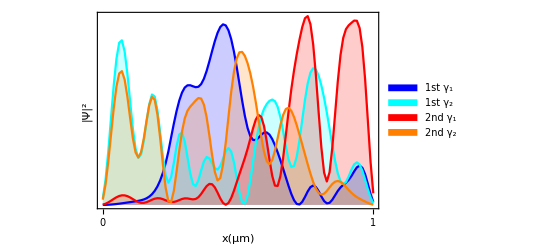

```mathematica
wfm=wfmajoranaseqd[1,1,.9,1.1,25,.2,{0.01356,0.048},3,100,2,FrameTicks->{None,{{0,1},None}},FrameLabel->{Style["x(μm)",Directive[Black,30]],Style["|Ψ|^2",Directive[Black,30]]},FrameTicksStyle->Directive[Black,30],PlotLabel->None]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp17\\bad-qd\\3\\m1.0D0.2a5L100VD1.1dL25g0.2Vc3.0V0.9.png",wfm]
```

D:\CMTC\bothlead\Rp17\bad-qd\3\m1.0D0.2a5L100VD1.1dL25g0.2Vc3.0V0.9.png

```mathematica
?wfmajoranamu
```

wfmajoranamu[a,μ,vz,mumax,sigma,dim,index]; WF for inhomogeneous potential, index for first one or two state(s)

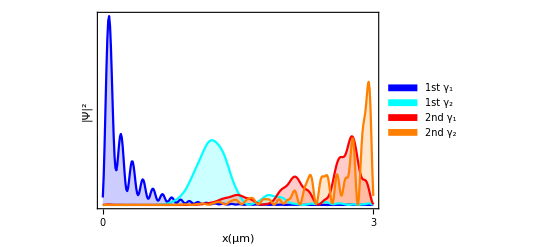

```mathematica
wfm=wfmajoranamu[1,1,.9,-1.1,50,300,2,FrameTicks->{None,{{0,3},None}},FrameLabel->{Style["x(μm)",Directive[Black,30]],Style["|Ψ|^2",Directive[Black,30]]},FrameTicksStyle->Directive[Black,30],PlotLabel->None]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp16\\bad-inhom\\3\\m1.0D0.2a5L300expmx-1.1sg50.0V0.9.png",wfm]
```

D:\CMTC\bothlead\Rp16\bad-inhom\3\m1.0D0.2a5L300expmx-1.1sg50.0V0.9.png

```mathematica
?wfmajoranasemu
```

wfmajoranasemu[a_,μ_,vz_,mumax_,sigma_,γ_,ω_,Vc_,dim_,index_]; WF for wfmajoranasemu[a_,μ_,vz_,mumax_,sigma_,γ_,ω_,Vc_,dim_,index_]

ω0=0.ω1=-0.00173744

ω0=0.054ω1=0.0546939

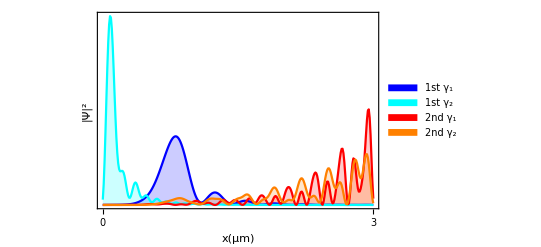

```mathematica
wfm=wfmajoranasemu[1,1,0.6,-1.1,50,0.2,{0.0,0.054},1,300,2,FrameTicks->{None,{{0,3},None}},FrameLabel->{Style["x(μm)",Directive[Black,30]],Style["|Ψ|^2",Directive[Black,30]]},FrameTicksStyle->Directive[Black,30],PlotLabel->None]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp16\\bad-inhom\\3\\m1.0D0.2a5L300expmx-1.1sg50.0g0.2Vc1.0V0.6.png",wfm]
```

D:\CMTC\bothlead\Rp16\bad-inhom\3\m1.0D0.2a5L300expmx-1.1sg50.0g0.2Vc1.0V0.6.png

```mathematica
SwatchLegend[{Blue,Cyan,Red,Orange},Style[#,Directive[Black,30]]&/@{"1st \!\(\*SubscriptBox[\(γ\), \(1\)]\)","1st \!\(\*SubscriptBox[\(γ\), \(2\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(1\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(2\)]\)"},LegendMarkerSize->30]
```

```mathematica
Export["swatchlegend.png",Out[177]]
```

swatchlegend.png

```mathematica
?wfmajoranadis
```

wfmajoranadis[a,μ,vz,vimplist,dim,index]; WF for disorder potential, index for first one or two state(s)

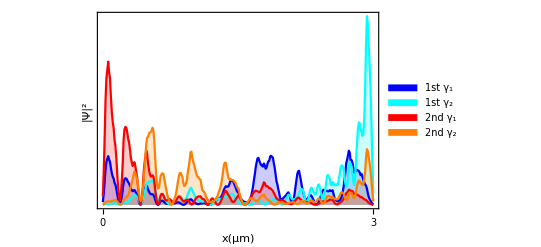

```mathematica
wfm=wfmajoranadis[1,1,.8,vimplist,300,2,FrameTicks->{None,{{0,3},None}},FrameLabel->{Style["x(μm)",Directive[Black,30]],Style["|Ψ|^2",Directive[Black,30]]},FrameTicksStyle->Directive[Black,30],PlotLabel->None]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp16\\ugly\\3\\m1.0D0.2a5L300v1.0V0.7.png",wfm]
```

D:\CMTC\bothlead\Rp16\ugly\3\m1.0D0.2a5L300v1.0V0.7.png

```mathematica
?wfmajoranasedis
```

wfmajoranasedis[a_,μ_,vz_,vimp_,γ_,ω_,dim_,index_]; WF for disorder in self energy model

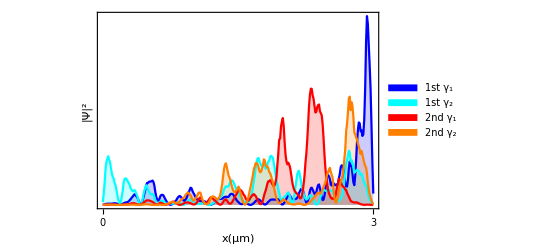

```mathematica
wfm=wfmajoranasedis[1,1,0.8,vimplist,.2,{0.0047,0.0374},1.2,300,2,FrameTicks->{None,{{0,3},None}},FrameLabel->{Style["x(μm)",Directive[Black,30]],Style["|Ψ|^2",Directive[Black,30]]},FrameTicksStyle->Directive[Black,30],PlotLabel->None]
```

```mathematica
Export["D:\\CMTC\\bothlead\\Rp16\\ugly\\3\\m1.0D0.2a5L300v1.0g0.2Vc3V0.7.png",wfm]
```

D:\CMTC\bothlead\Rp16\ugly\3\m1.0D0.2a5L300v1.0g0.2Vc3V0.7.png

```mathematica
h
```

```mathematica
es=Eigensystem[Hseqd[1,1,.7,1.7,20,.2,.0060,3,100],-6,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}];
```

```mathematica
Clear[es]
```

```mathematica
es[[1]]
```

{-0.826271,0.817749,-0.668406,0.659884,-0.658434,0.649912,-0.541739,0.533217,-0.477603,0.46908,-0.315694,0.307172,-0.283284,0.274761,-0.21249,0.203967,-0.172342,0.16382,-0.126952,0.11843}

```mathematica
ii
```

9

```mathematica
wfmajoranasemu[a_,μ_,vz_,mumax_,sigma_,γ_,ω_,Vc_,dim_?IntegerQ,index_?IntegerQ]:=Block[{testp,testn,g,gamma,test,gamma1,gamma2,(*,es*)},g=Table[es=Eigensystem[Hsemu[a,μ,vz,mumax,sigma,γ,ω⟦i⟧,Vc,dim],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}];ii=Nearest[es[[1]]->Automatic,ω[[i]],1][[1]];testp=es[[All,ii]];If[Abs[ω[[i]]-testp[[1]]]>10^-4,Print["ω0=",ω[[i]],"ω1=",testp[[1]]]];gamma=KroneckerProduct[1/2 ConjugateTranspose[{{1,ⅈ,0,0},{0,0,1,ⅈ},{0,0,1,-ⅈ},{-1,ⅈ,0,0}}],IdentityMatrix[dim,SparseArray]].testp⟦2⟧;{Total[ArrayReshape[Abs[gamma]^2,{4,dim}]⟦{1,3}⟧],Total[ArrayReshape[Abs[gamma]^2,{4,dim}]⟦{2,4}⟧]},{i,index}];gamma1=g⟦All,1⟧;gamma2=g⟦All,2⟧;ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma1,gamma2}]],1],DataRange->{0,(dim a)/100},PlotLabel->"\!\(\*SubscriptBox[\(V\), \(Z\)]\)="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,Filling->Axis,PlotLegends->Placed[SwatchLegend[{"1st \!\(\*SubscriptBox[\(γ\), \(1\)]\)","1st \!\(\*SubscriptBox[\(γ\), \(2\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(1\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(2\)]\)"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->{Blue,Cyan,Red,Orange}]]
```

```mathematica
Hsemu[a_?NumberQ,μ0_?NumberQ,V0_?NumberQ,mumax_,sigma_,γ_,ω_,Vc_,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=5/(2 a),Vz=V0,Δ=.2,mux},mux=mumax Exp[-#1^2/(2 sigma^2)]+μ&;Δ=If[V0<Vc,Δ √(1-(V0/Vc)^2),0];KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}]+(2 t) IdentityMatrix[dim,SparseArray]-DiagonalMatrix[SparseArray[mux[Range[dim]-1]]]]+KroneckerProduct[PauliMatrix[2],ⅈ α SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}]]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz IdentityMatrix[dim,SparseArray]]]-γ Re[(ω IdentityMatrix[4 dim,SparseArray])/(√(Δ^2-ω^2-ⅈ/10^9))+KroneckerProduct[PauliMatrix[1],KroneckerProduct[IdentityMatrix[2],(Δ IdentityMatrix[dim,SparseArray])/(√(Δ^2-ω^2-ⅈ/10^9))]]]]
```

```mathematica
wfmajoranasedis[a_,μ_,vz_,vimp_,γ_,ω_,Vc_,dim_?IntegerQ,index_]:=Block[{testp,testn,g,gamma,test,gamma1,gamma2,es,ii},If[Length[vimp]≠dim,Message[wfmajoranasedis::nnarg,Length[vimp],dim];Throw[$Failed]];g=Table[es=Eigensystem[Hsedis[a,μ,vz,vimp,γ,ω⟦i⟧,Vc,dim],-6,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}];ii=Nearest[es[[1]]->Automatic,ω[[i]],1][[1]];testp=es[[All,ii]];If[Abs[ω⟦i⟧-testp⟦1⟧]>1/10^4,Print["ω0=",ω⟦i⟧,"ω1=",testp⟦1⟧]];gamma=KroneckerProduct[1/2 ConjugateTranspose[{{1,ⅈ,0,0},{0,0,1,ⅈ},{0,0,1,-ⅈ},{-1,ⅈ,0,0}}],IdentityMatrix[dim,SparseArray]].testp⟦2⟧;{Total[ArrayReshape[Abs[gamma]^2,{4,dim}]⟦{1,3}⟧],Total[ArrayReshape[Abs[gamma]^2,{4,dim}]⟦{2,4}⟧]},{i,index}];gamma1=g⟦All,1⟧;gamma2=g⟦All,2⟧;ListLinePlot[Flatten[Transpose[ArrayFlatten[{gamma1,gamma2}]],1],DataRange->{0,(dim a)/100},PlotLabel->"\!\(\*SubscriptBox[\(V\), \(Z\)]\)="<>ToString[vz]<>"(meV)",PlotRange->Full,Frame->True,Filling->Axis,PlotLegends->Placed[SwatchLegend[{"1st \!\(\*SubscriptBox[\(γ\), \(1\)]\)","1st \!\(\*SubscriptBox[\(γ\), \(2\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(1\)]\)","2nd \!\(\*SubscriptBox[\(γ\), \(2\)]\)"}],Top],FrameLabel->{"x(μm)",""},PlotStyle->{Blue,Cyan,Red,Orange}]]
```